```mathematica
(*Зададим данную функцию и построим ее график*)
f[x_,y_]=3*x^2*y+y^3-12*x-15*y+3;
Plot3D[f[x,y],{x,-5,5},{y,-5,5},PlotRange->Full]
```

-Graphics3D-

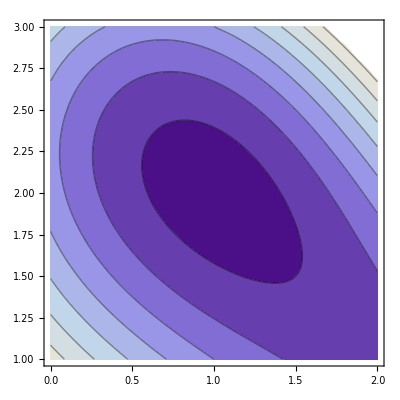

```mathematica
(*Локализуем точку минимума данной функции*)
(*Построим линии уровня данной функции в окрестности точки минимума*)
GC=ContourPlot[f[x,y],{x,0,2},{y,1,3}]
```

```mathematica
(*Построим график функции в окрестности точки минимума*)
G=Plot3D[f[x,y],{x,0,2},{y,1,3},PlotRange->Full]
```

-Graphics3D-

```mathematica
(*Зададим точность вычислений*)
eps=10^(-5);
(*Найдем нормированный вектор градиента заданной функции*)
n[x_,y_]=Grad[f[x,y],{x,y}]/Norm[Grad[f[x,y],{x,y}]];
(*Зададим начальное приближение к точке минимума*)
M0={2,3};
(*Зададим длину шага приближения к точке минимума*)
lambda=1;
(*Зададим счетчик итераций*)
k=0;
(*Зададим последовательность итераций*)
IT={Join[M0,{f[M0[[1]],M0[[2]]]}]};
(*Реализуем алгоритм градиентного метода поиска точки минимума*)
While[lambda≥eps,
M1=M0-lambda*N[n[M0[[1]],M0[[2]]]];
If[f[M1[[1]],M1[[2]]]>f[M0[[1]],M0[[2]]],
lambda=lambda/2,
M0=M1;
k=k+1;
AppendTo[IT,Join[M0,{f[M1[[1]],M1[[2]]]}]]
];
];
(*Найдем последнее приближение к точке минимума*)
M1=M0-lambda*N[n[M0[[1]],M0[[2]]]];
k=k+1;
AppendTo[IT,Join[M0,{f[M1[[1]],M1[[2]]]}]];
Print["Точка минимума функции равна: ",M1]
Print["Значение функции в точке минимума равно: ",f[M1[[1]],M1[[2]]]]
Print["Количество приближений к точке минимума равно: ",k]
```

Точка минимума функции равна: {1.,2.}

Значение функции в точке минимума равно: -25.

Количество приближений к точке минимума равно: 11

```mathematica
(*Построим график данной функции и последовательности приближений к точке минимума в одной системе координат*)
GIT3D=ListPointPlot3D[IT,PlotStyle->Red];
Show[G,GIT3D]
```

-Graphics3D-

```mathematica
(*Выполним анимацию последовательности приближений к точке минимума данной функции*)
Animate[Show[G,ListPointPlot3D[{IT[[i]]},PlotStyle->Red]],{i,1,k+1,1},AnimationRunning->False]
```

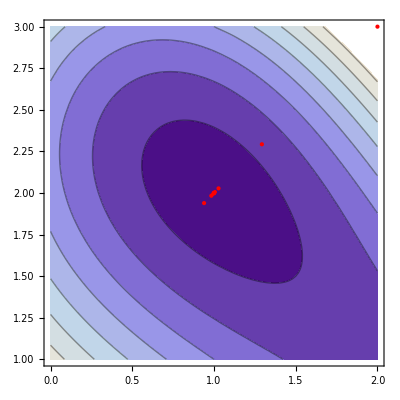

```mathematica
(*Построим линии уровня и последовательность приближений к точке минимума данной функции *)
ITC=Table[{IT[[i,1]],IT[[i,2]]},{i,1,k+1}];
GIT=ListPlot[ITC,PlotStyle->Red];
Show[GC,GIT]
```

```mathematica
(*Выполним анимацию последовательности приближений к точке минимума данной функции на графике линий уровня данной функции*)
Animate[Show[GC,ListPlot[{ITC[[i]]},PlotStyle->Red]],{i,1,k+1,1},AnimationRunning->False]
```